```mathematica
№2022080
```

1. ParametricPlot — строит график кривых, задаваемых параметрически X=X(t), Y=Y(t).

```mathematica
ParametricPlot[{Sin[u],Sin[2u]},{u,0,5 Pi}]
```

```mathematica
Animate[ParametricPlot[{Sin[u],a  Sin[2u]},{u,0,2 Pi}],{a,-11,27},AnimationRunning->False]
```

```mathematica
ListAnimate[Table[ParametricPlot[{Sin[u],a  Sin[2u]},{u,0,2 Pi}],{a,0,}]]
```

2. ParametricPlot3D — функция для построения трехмерных кривых и трехмерных поверхностей,

```mathematica
ParametricPlot3D[{ Sin[u],Cos[u ],u/10},{u,0,20}]
```

```mathematica
Animate[ParametricPlot3D[{a Sin[u],Cos[u +2a],u/10},{u,0,20}],{a,0,10},AnimationRunning->False]
```

```mathematica
ListAnimate[Table[ParametricPlot3D[{a Sin[u],Cos[u +2a],u/10},{u,0,20}],{a,0,4}]]
```

3. ContourPlot — функция для построения графиков кривых, заданных неявным уравнением (Эта функция похожа на Plot, только вместо явного выражения,содержащего одну переменную, вы задаете уравнение, содержащее две переменных),

```mathematica
ContourPlot[Cos[x]+Cos[y],{x,0,4Pi},{y,0,4Pi}]
```

```mathematica
Animate[ContourPlot[Cos[x + 23a]+ 34 Cos[y] a,{x,0,4Pi},{y,0,4Pi}],{a,0,1},AnimationRunning->False]
```

```mathematica
ListAnimate[Table[ContourPlot[Cos[x + 24a]+Cos[y] a,{x,0,4Pi},{y,0,2Pi}],{a,0,1}]]
```

4. Plot —  с помощью этой функции строится график функции, заданной явным уравнением y=f(x),

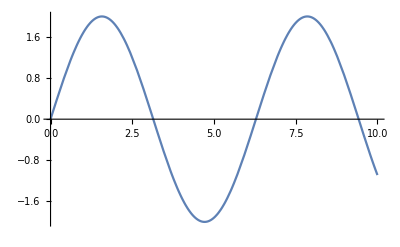

```mathematica
Plot[Sin[x]+Sin[x],{x,0,10},PlotRange->2]
```

```mathematica
Animate[Plot[Sin[a+x]+Sin[x-a],{x,0,10},PlotRange->2],{a,1,5},AnimationRunning->False]
```

```mathematica
ListAnimate[Table[Plot[Sin[a+x]+Sin[x-a],{x,0,10},PlotRange->2],{a,1,5}]]
```

5.ContourPlot3D — эта функция предназначена для построения поверхностей постоянного значения (поверхностей уровня) функций трех переменных ,

```mathematica
ContourPlot3D[x^3 + 2 +y^2-z^2 ,{x,-2,2},{y,-2,2},{z,-2,2}]
```

```mathematica
Animate[ContourPlot3D[x^3 + 2 a+y^2-z^a 2 ,{x,-2,2},{y,-2,2},{z,-2,2}],{a,1,2},AnimationRunning->False]
```

```mathematica
ListAnimate[Table[ContourPlot3D[x^3 + 2 a+y^2-z^a 2 ,{x,-2,2},{y,-2,2},{z,-2,2}],{a,1,2}]]
```

6. Plot3D — функция предназначена для построения поверхности функции z=f(x,y),

```mathematica
Plot3D[Cos[x^2+y^2] E^(-x/2-y/2),{x,-1.5,2},{y,-1.5,2}]
```

```mathematica
Animate[Plot3D[Cos[(x+a)^2+y^2-a] E^(-x/2-y/2),{x,-1.5,2},{y,-1.5,2}],{a,1,2},AnimationRunning->False]
```

```mathematica
ListAnimate[Table[Plot3D[Cos[(x+a)^2+y^2-a] E^(-x/2-y/2),{x,-1.5,2},{y,-1.5,2}],{a,1,2}]]
```

7. DiscretePlot — создаёт график последовательностей,

```mathematica
DiscretePlot[PrimePi[k],{k,1,20}]
```

```mathematica
Animate[DiscretePlot[PrimePi[k],{k,a,20}],{a,2,7},AnimationRunning->False]
```

```mathematica
ListAnimate[Table[DiscretePlot[PrimePi[k],{k,a,20}],{a,2,7}]]
```

8. PlotLayout — опция, используемая для указания макета нескольких графиков.

```mathematica
WaveletListPlot[StationaryWaveletTransform[Sin[Range[30]^2/50],Automatic,3],PlotLayout->"CommonXAxis"]
```

```mathematica
Animate[WaveletListPlot[StationaryWaveletTransform[Sin[Range[30+a]^2/50],Automatic,3],PlotLayout->"CommonXAxis"],{a,2,70},AnimationRunning->False]
```

```mathematica
ListAnimate[Table[WaveletListPlot[StationaryWaveletTransform[Sin[Range[30+a]^2/50],Automatic,3],PlotLayout->"CommonXAxis"],{a,2,70}]]
```

9. DiscretePlot3D — строит трехмерный график значений выражения функции,

```mathematica
DiscretePlot3D[PDF[MultivariatePoissonDistribution[3,{1,1}],{t,u}],{t,1,10},{u,0,1},ExtentSize->Full]
```

```mathematica
Animate[DiscretePlot3D[PDF[MultivariatePoissonDistribution[3,{1,1}],{t,u}],{t,1,10},{u,0,a},ExtentSize->Full],{a,0,10},AnimationRunning->False]
```

```mathematica
ListAnimate[Table[DiscretePlot3D[PDF[MultivariatePoissonDistribution[3,{1,1}],{t,u}],{t,1,10},{u,0,a},ExtentSize->Full],{a,0,10}]]
```

10. PlotLegends — это опция для функций сюжета, определяющая, какие легенды использовать.

```mathematica
Plot[{1/2- Sin[x],Cos[x]},{x,0,2π},PlotLegends->Automatic]
```

```mathematica
Animate[Plot[{1/2a- Sin[x],Cos[x+a]},{x,0,2π},PlotLegends->Automatic],{a,0,10},AnimationRunning->False]
```

```mathematica
ListAnimate[Table[Plot[{1/2a- Sin[x],Cos[x+a]},{x,0,2π},PlotLegends->Automatic],{a,0,10}]]
```

11. PlotPoints — это опция для построения графиков функций, указывающая, сколько точек начальной выборки следует использовать (по умолчанию равная 50).

```mathematica
Plot3D[Sin[x y],{x,0,2},{y,0,2},PlotPoints->10,Mesh->All,MaxRecursion->0]
```

```mathematica
Animate[Plot3D[Sin[x y a],{x,0,2},{y,0,2},PlotPoints->10,Mesh->All,MaxRecursion->0],{a,0,10},AnimationRunning->False]
```

```mathematica
ListAnimate[Table[Plot3D[Sin[x y a],{x,0,2},{y,0,2},PlotPoints->10,Mesh->All,MaxRecursion->0],{a,0,10}]]
```

12. GraphPlot — генерирует график графика,

```mathematica
GraphPlot[{1->2,2->1,3->1,3->2,4->1,4->2,4->4},VertexLabeling->True]
```

```mathematica
Animate[GraphPlot[{1->2a,2->1,3->1,3->2,4->1,4->2,4->a},VertexLabeling->True], {a,0,13},AnimationRunning->False]
```

```mathematica
ListAnimate[Table[GraphPlot[{1->2a,2->1,3->1,3->2,4->1,4->2,4->a},VertexLabeling->True], {a,0,13}]]
```

13. PlotRange — опция для графических функций, указывающая, какой диапазон координат включать в график,

```mathematica
Plot[Tan[x],{x,0,10},PlotRange->Automatic]
```

```mathematica
Animate[Plot[Tan[x+a],{x,0,10},PlotRange->Automatic], {a,0,13},AnimationRunning->False]
```

```mathematica
ListAnimate[Table[Plot[Tan[x+a],{x,0,10},PlotRange->Automatic], {a,0,7}]]
```

14. GraphPlot3D — генерирует трехмерный график графика,

```mathematica
GraphPlot3D[{1->2,1->3,1->4,1->5,2->3,2->4,2->5,3->4,3->5,4->5}]
```

```mathematica
Animate[GraphPlot3D[{1->2,1->a,1->2a,1->5,2->3,2->4,2->5,3->4,3->5,4->5}], {a,0,13},AnimationRunning->False]
```

```mathematica
ListAnimate[Table[GraphPlot3D[{1->2,1->a,1->2a,1->5,2->3,2->4,2->5,3->4,3->5,4->5}, VertexLabeling->True],{a,0,13}]]
```

15. PlotRangeClipping — это опция для графических функций, которая указывает, должны ли графические объекты обрезаться по краю области, определенной PlotRange, или разрешено расширяться до края изображения.

```mathematica
Graphics[{Pink,Disk[{0,0},5]},Frame->True,PlotRange->4,PlotRangeClipping->False]
```

```mathematica
Animate[Graphics[{Pink,Disk[{a,0},5-a]},Frame->True,PlotRange->4,PlotRangeClipping->False], {a,1,2},AnimationRunning->False]
```

16. ListContourPlot — упорядочивает последовательные строки массива вверх по странице и последовательные столбцы,

```mathematica
ListContourPlot[Table[Sin[i+j^2],{i,0,3,0.1},{j,0,3,0.1}]]
```

```mathematica
Animate[ListContourPlot[Table[Sin[a i+j^2a],{i,0,3,0.1},{j,0,3,0.1}]], {a,2,7},AnimationRunning->False]
```

```mathematica
ListAnimate[Table[ListContourPlot[Table[Sin[a i+j^2a],{i,0,3,0.1},{j,0,3,0.1}]],  {a,2,7}]]
```

16.2 PlotStyle — это опция для построения и связанных функций, которая определяет стили, в которых должны быть нарисованы объекты,

```mathematica
Plot[Evaluate@Table[BesselJ[n,x],{n,3}],{x,0,15},PlotStyle->{Orange,Dashed,Thick}]
```

```mathematica
Animate[Plot[Evaluate@Table[BesselJ[n+a,x],{n,3}],{x,0,15},PlotStyle->{Orange,Dashed,Thick}], {a,2,7},AnimationRunning->False]
```

```mathematica
ListAnimate[Table[Plot[Evaluate@Table[BesselJ[n+a,x],{n,3}],{x,0,15},PlotStyle->{Orange,Dashed,Thick}], {a,2,7}]]
```

17. ListContourPlot3D — генерирует контурный график из трехмерного массива значений.

```mathematica
ListContourPlot3D[Table[x^2+y^2-z^2+RandomReal[0.1],{x,-2,2,0.2},{y,-2,2,0.2},{z,-2,2,0.2}],Contours->3,Mesh->None]
```

```mathematica
Animate[ListContourPlot3D[Table[x^2a+y^2-z a^2+RandomReal[0.1],{x,-2,2,0.2},{y,-2,2,0.2},{z,-2,2,0.2}],Contours->3,Mesh->None], {a,1,3},AnimationRunning->False]
```

```mathematica
ListAnimate[Table[ListContourPlot3D[Table[x^2a+y^2-z a^2+RandomReal[0.1],{x,-2,2,0.2},{y,-2,2,0.2},{z,-2,2,0.2}],Contours->3,Mesh->None], {a,1,3}]]
```

18. PolarPlot — генерирует полярный график кривой с указанным радиусом как функцию указанного угла,

```mathematica
PolarPlot[Sin[3t],{t,0,Pi}]
```

```mathematica
Animate[PolarPlot[Sin[3t+a],{t,0,Pi}], {a,1,10},AnimationRunning->False]
```

```mathematica
ListAnimate[Table[PolarPlot[Sin[3t+a],{t,0,Pi}], {a,1,10}]]
```

19. ListLinePlot — рисует линию через указанные точки

```mathematica
ListLinePlot[Prime[Range[25]],Filling->Axis]
```

```mathematica
Animate[ListLinePlot[Prime[Range[25+2a]],Filling->Axis], {a,2,15},AnimationRunning->False]
```

```mathematica
ListAnimate[Table[ListLinePlot[Prime[Range[25+2a]],Filling->Axis], {a,2,15}]]
```

20. RegionPlot —  строит график, показывающий область, определенную неравенством.

```mathematica
RegionPlot[x^2+y^3<2,{x,-2,2},{y,-2,2}]
```

```mathematica
Animate[RegionPlot[x^2+y^3<2+8a,{x,-2,2},{y,-2,2}], {a,0,1},AnimationRunning->False]
```

```mathematica
ListAnimate[Table[RegionPlot[x^2+y^3<2+8a,{x,-2,2},{y,-2,2}], {a,0,1}]]
```

21. TreePlot — генерирует древовидный график указанного графика,

```mathematica
TreePlot[{1->4,1->6,1->8,2->6,3->8,4->5,7->8},VertexLabeling->True]
```

```mathematica
Animate[TreePlot[{1+a->4,1->6,1->8-a,2->6,3a->8,4->5,2a->8},VertexLabeling->True], {a,0,10},AnimationRunning->False]
```

```mathematica
ListAnimate[Table[TreePlot[{1+a->4,1->6,1->8-a,2->6,3a->8,4->5,2a->8},VertexLabeling->True], {a,0,10}]]
```

22. VectorPlot — генерирует векторный график векторного,

```mathematica
VectorPlot[{{y,-x},{x,y}},{x,-3,3},{y,-3,3}]
```

```mathematica
Animate[VectorPlot[{{y,x+2a},{a x,a-y}},{x,-3,3},{y,-3,3}], {a,2,22},AnimationRunning->False]
```

```mathematica
ListAnimate[Table[VectorPlot[{{y,x+2a},{a x,a-y}},{x,-3,3},{y,-3,3}], {a,2,22}]]
```

23. ListVectorPlot3D — генерирует трехмерный векторный график из трехмерного массива значений векторного поля,

```mathematica
ListVectorPlot3D[Table[{{x,y,z},{y,x-x^3,z}},{x,-1.5,1.5,0.2},{y,-2,2,0.2},{z,-1,1,0.1}]]
```

```mathematica
Animate[ListVectorPlot3D[Table[{{x,y,z},{y-a,x-(x+2a)^3,z}},{x,-1.5,1.5,0.2},{y,-2,2,0.2},{z,-1,1,0.1}]], {a,0,10},AnimationRunning->False]
```

```mathematica
ListAnimate[Table[ListVectorPlot3D[Table[{{x,y,z},{y-a,x-(x+2a)^3,z}},{x,-1.5,1.5,0.2},{y,-2,2,0.2},{z,-1,1,0.1}]], {a,0,10}]]
```

24. VectorPlot3D — генерирует трехмерный векторный график векторного поля.

```mathematica
VectorPlot3D[{x,y,z},{x,-1,1},{y,-1,1},{z,-1,1}]
```

```mathematica
Animate[VectorPlot3D[{x+a,y a,z-a},{x,-1,1},{y,-1,1},{z,-1,1}], {a,0,10},AnimationRunning->False]
```

```mathematica
ListAnimate[Table[VectorPlot3D[{x+a,y a,z-a},{x,-1,1},{y,-1,1},{z,-1,1}], {a,0,10}]]
```